## Ref: https://arxiv.org/pdf/0706.2210.pdf

#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];
LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

```mathematica
NotebookDirectory[]//SetDirectory;
<<"/home/wei-chih/Desktop/Research/7o/7o_master_file.m"
```

```mathematica
ReadInDMFile[DensityMatrixFile_]:=Block[{},
inputstring=Import[DensityMatrixFile,"TSV"];
DensityMatrixVector={};
For[i=1,i<=Length[inputstring],i++,
JT=StringCases[inputstring[[i,1]],RegularExpression["ONE.+JO.+\\s(\\d+)\\s.+(\\d+).*"]->{"$1","$2"}]//ToExpression;
dens=StringCases[inputstring[[i,1]],RegularExpression["(\\d+)\\s+(\\d+)\\s+(\\d+)\\s+(\\d+)\\s+(.+\\d+.\\d+).+"]->{"$1","$2","$3","$4","$5"}]//ToExpression;
If[{}!=JT,oJT=JT[[1]]/2;];
If[{}!=dens,oDens={dens[[1,5]],{dens[[1,1]],dens[[1,2]]/2},{dens[[1,3]],dens[[1,4]]/2},oJT[[1]],oJT[[2]]};DensityMatrixVector=DensityMatrixVector~Join~{oDens}];];

For[i=1,i<=Length[DensityMatrixVector],i++,
DensityMatrix[i]=DensityMatrixVector[[i]];];
SetDMmatrixLength[Length[DensityMatrixVector]];
Return[];];
```

### Constant

```mathematica
ΔEs={0.0,1.11834,2.05405,2.34664,2.48519,2.54724,3.19444,3.24109,3.25989,3.34722,3.35640,3.51955,3.64413,3.73187,3.75969,3.87191};
SpinJs={0,2,4,2,6,2,0,3,1,3,4,5,4,2,0,2};
   
(*2~16*)
Ar40={"Ar",18,40,0,"DMfiles/ar40_obdm2.dat"};
ΔE=ΔEs⟦2⟧ 10^-3;
SpinJ=SpinJs⟦2⟧;
OutputNameNC="pointsNC/dm2.csv";

evenJ=EvenQ[SpinJ];
If[SpinJ==0,J0=0,J0=1];
```

```mathematica
Subscript[ϵ, χ]=10^-4;
Subscript[α, D]=0.5;
Subscript[g, D]=√(4π Subscript[α, D]);
e=0.30282212;

Nucleus=Ar40;
mN=0.938;
mA=Nucleus⟦3⟧ mN;
Ji=Nucleus⟦4⟧;
me=0.5110 10^-3;
mπ=0.139;
mμ=0.1056;
GF=1.166 10^-5;
Subscript[g, A]=1.258;
Subscript[M, A]=1.05;
F1=1;
FA=-Subscript[g, A];
FP=(2 mN FA)/(mπ^2-q^2);
μ1=4.706;
GeVcm=(6.5821 10^-25) (3 10^10);
sinΘc=0.22;
sin2Θw=0.2229;
cosΘc=√(1-sinΘc^2);
ℏ𝒸=0.197;
alpha=1/137;
qVp=0.01556533;
qVn=-0.5122125;
b[A_]:=√(41.467/(45 A^(-1/3)-25 A^(-2/3)));
yy[q_,A_]:= ((q b[A])/(2ℏ𝒸))^2;
```

### Read density matrix file

```mathematica
NotebookDirectory[]//SetDirectory;
ReadInDMFile[Nucleus⟦5⟧];
```

```mathematica
ΨJ2T0=Select[DensityMatrixVector,(#[[5]]==0)&];
ΨJ2T1=Select[DensityMatrixVector,(#[[5]]==1)&];
```

```mathematica
ThreeJSymbol[{2,-2},{0,0},{2,2}]
ThreeJSymbol[{2,-2},{1,0},{2,2}]
```

1/(√5)

√(2/15)

```mathematica
ΨJ2T0[[All,1]]=ΨJ2T0[[All,1]]/√5;
ΨJ2T1[[All,1]]=ΨJ2T1[[All,1]] √(2/15);
```

### Multipole Operator

```mathematica
M[y_,{Np_,jp_},{N_,j_},J_]:=F1 MJ[y,{Np,jp},{N,j},J];
M5[y_,{Np_,jp_},{N_,j_},J_]:=(I q)/mN (FA  OmegaPJ[y,{Np,jp},{N,j},J]+(ω FP)/2 SigmaPPJ[y,{Np,jp},{N,j},J]);
L[y_,{Np_,jp_},{N_,j_},J_]:=ω/q M[y,{Np,jp},{N,j},J]J0;
L5[y_,{Np_,jp_},{N_,j_},J_]:=I (FA - q^2/(2mN)FP)SigmaPPJ[y,{Np,jp},{N,j},J] ;
Subscript[T, el][y_,{Np_,jp_},{N_,j_},J_]:=q/mN( F1 DeltaPJ[y,{Np,jp},{N,j},J]+1/2 μ1 SigmaJ[y,{Np,jp},{N,j},J])J0;
Subscript[T, el5][y_,{Np_,jp_},{N_,j_},J_]:=I FA SigmaPJ[y,{Np,jp},{N,j},J];
Subscript[T, mag][y_,{Np_,jp_},{N_,j_},J_]:=-(I q)/mN(F1 DeltaJ[y,{Np,jp},{N,j},J]-μ1/2 SigmaPJ[y,{Np,jp},{N,j},J]);
Subscript[T, mag5][y_,{Np_,jp_},{N_,j_},J_]:=FA SigmaJ[y,{Np,jp},{N,j},J]J0;
```

```mathematica
SummedM[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*M[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedM5[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*M5[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedL[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*L[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedL5[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*L5[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, el][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, el][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, el5][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, el5][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, mag][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, mag][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, mag5][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, mag5][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
```

Calculate the three terms governing the nuclear response (see Eq. (33)), removing the common term e^(-2y).

```mathematica
ΨJ2T=ΨJ2T0;
```

```mathematica
MTerm[y_]:=Simplify[Exp[2 y]SummedM[y,ΨJ2T]Conjugate[SummedM[y,ΨJ2T]],{q,ω,y}∈ Reals];
MTerm5[y_]:=Simplify[Exp[2 y]SummedM5[y,ΨJ2T]Conjugate[SummedM5[y,ΨJ2T]],{q,ω,y}∈ Reals];

LTerm[y_]:=Simplify[Exp[2 y]SummedL[y,ΨJ2T]Conjugate[SummedL[y,ΨJ2T]],{q,ω,y}∈ Reals];
LTerm5[y_]:=Simplify[Exp[2 y]SummedL5[y,ΨJ2T]Conjugate[SummedL5[y,ΨJ2T]],{q,ω,y}∈ Reals];


LMTerm[y_]:=Simplify[Exp[2 y]Re[SummedL[y,ΨJ2T]Conjugate[SummedM[y,ΨJ2T]]],{q,ω,y}∈ Reals];
LMTerm5[y_]:=Simplify[Exp[2 y]Re[SummedL5[y,ΨJ2T]Conjugate[SummedM5[y,ΨJ2T]]],{q,ω,y}∈ Reals];

TTerm[y_]:=Simplify[Exp[2 y](Subscript[SummedT, mag5][y,ΨJ2T]  Conjugate[Subscript[SummedT, mag5][y,ΨJ2T]]+Subscript[SummedT, el][y,ΨJ2T]  Conjugate[Subscript[SummedT, el][y,ΨJ2T]]),{q,ω,y}∈ Reals];
TTerm5[y_]:=Simplify[Exp[2 y](Subscript[SummedT, mag][y,ΨJ2T]  Conjugate[Subscript[SummedT, mag][y,ΨJ2T]]+Subscript[SummedT, el5][y,ΨJ2T]  Conjugate[Subscript[SummedT, el5][y,ΨJ2T]]),{q,ω,y}∈ Reals];
```

### DM currents

```mathematica
mχ=30 10^-3;
Subscript[p, χ][E_]:=√(E^2-mχ^2);
l00[Eχ_,q_]:=Max[1+1/(4Eχ(Eχ-ΔE))(2(Subscript[p, χ][Eχ])^2+2(Subscript[p, χ][Eχ-ΔE])^2-2 q^2+ mχ^2),0];
l33[Eχ_,q_]:=Max[1+1/(Eχ(Eχ-ΔE))(-3/2(Subscript[p, χ][Eχ])^2-3/2(Subscript[p, χ][Eχ-ΔE])^2+3/2 q^2-mχ^2/4),0];
l30[Eχ_,q_]:=-(((Subscript[p, χ][Eχ])^2+(Subscript[p, χ][Eχ-ΔE])^2-q^2)/(2 Subscript[p, χ][Eχ] (Eχ-ΔE)))-(Subscript[p, χ][Eχ])/Eχ;
ldotl[Eχ_,q_]:=Max[3-1/(Eχ(Eχ-ΔE))(1/2((Subscript[p, χ][Eχ])^2+(Subscript[p, χ][Eχ-ΔE])^2-q^2)+3/4 mχ^2),0];
```

```mathematica
XsectionNC0[Eχ_,y_]:=Exp[-2 y](l00[Eχ,q]MTerm[y]+l33[Eχ,q]LTerm[y] -2l30[Eχ,q] LMTerm[y]+1/2(ldotl[Eχ,q]-l33[Eχ,q])TTerm[y]);

XsectionNC5[Eχ_,y_]:= Exp[-2 y](l00[Eχ,q]MTerm5[y]+l33[Eχ,q]LTerm5[y] -2l30[Eχ,q] LMTerm5[y]+1/2(ldotl[Eχ,q]-l33[Eχ,q])TTerm5[y]);
```

### |cosθ|<1 constraint

```mathematica
ErTolerance=.005;(*to avoid numerical error and imaginary number*)
ErMax[Eχ_]:=(Subscript[p, χ][Eχ]+Subscript[p, χ][Eχ-ΔE])^2/(2mA)(1-ErTolerance);
ErMin[Eχ_]:=(Subscript[p, χ][Eχ]-Subscript[p, χ][Eχ-ΔE])^2/(2mA)(1+ErTolerance);
```

```mathematica
XsectionNC[Eχ_,y_]:=If[evenJ,XsectionNC0[Eχ,y],XsectionNC5[Eχ,y]];
```

```mathematica
dσdErInelasticNC[ER_,Eχ_]=(2 e^2 Subscript[ϵ, χ]^2 Subscript[g, D]^2 (Eχ-ΔE)^2)/(Subscript[p, χ][Eχ]Subscript[p, χ][Eχ-ΔE](2 mA ER+(3mχ)^2)^2)mA/(2π)(4π)/(2Ji+1)XsectionNC[Eχ,yy[q,Nucleus⟦3⟧]]/.{ω->(ΔE),q->√(2mA ER)};
```

```mathematica
σInelasticNC[Eχ_]:=If[Eχ>ΔE+mχ,NIntegrate[dσdErInelasticNC[ER,Eχ],{ER,ErMin[Eχ],ErMax[Eχ]}],0];
```

```mathematica
pointsNC=Table[{EχMeV,GeVcm^2 σInelasticNC[EχMeV 10^-3]},{EχMeV,Range[1,100,2]}];
(*Export[OutputNameNC,pointsNC];*)
```

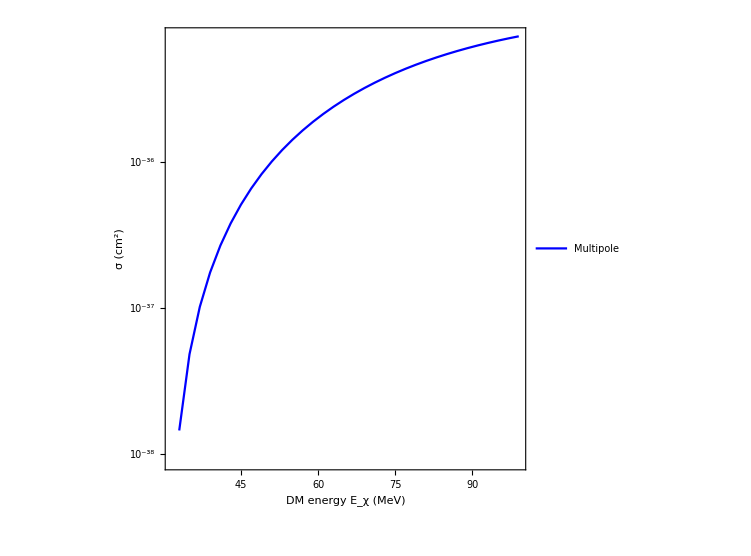

```mathematica
ListLogPlot[{pointsNC},Joined->True,PlotStyle->{Blue, Green},PlotLegends->Legend[{"Multipole", "T1"},Position->{0.75,0.2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Black]&)],FrameLabel->{"DM energy E_χ (MeV)", "σ (cm^2)"}]
```